```mathematica
Clear["Global`*"]
βzn=0.12;(*zombie-worker attack rate*)
βmz=0.05;(*zombie-mole attack rate*)
βzp=0.1;(*zombie-pet attack rate*)
βpw=0.1;(*zombiepet-worker attack rate*)
βzm=0.12;(*zombie-soldier attack rate*)
βm=0.14;(*zombiepet-soldier attack rate*)
βhm = 0.08;(*zombiepet-mole attack rate*)
δzn=0.1;(*worker-zombie attack rate*)
δzm=0.45;(*soldier-zombie attack rate*)
δzp=0.08;(*worker-zombiepet attack rate*)
δzmp=0.12;(*soldier-zombiepet attack rate*)
δs = 0.001; (*birthrate for averge people*)
γ = 0.03;(*worker to soldier*)
γ1= 1;(*ratio Sacrifice*)
Fhm = 0.4;(*resource consumption mole*)
Fw = 1;(*resource consumption worker*)
Fm = 1.5;(*resource consumption soldier*)
k = 1;

F[x_]:=1/2+1/2 Tanh[k*x];  (*Heaviside approximation using tanh*)
DFL[t_]:=R[t]/(Fhm*Shm[t]/S[t]+Fw*Shw[t]/S[t]+Fm*Sm[t]/S[t]);

f1[t_]:=0.5*F[3-DFL[t]];


eqs={Szn'[t]==(βzn Shw[t]Szn[t])(*bite worker*)+βzm * Sm[t]Szn[t] (*bite soldier*)+ βmz * Shm[t]Szn[t]-δzn  * Shw[t]Szn[t](*killed by worker*)-δzm * Sm[t]Szn[t] (*killed by soldier*)-δd * Szn[t],
Szp'[t]==βzp * Sp[t] Szn[t](*bite by zombie*)-δzp  * Shw[t]Szp[t](*killed by worker*)- δzmp * Szp[t]Sm[t](*killed by soldier*),
Shw'[t]==(-βzn  Szn[t]Shw[t](*killed by zombie*)- βzp * Szp[t]Shw[t](*killed by zombiepet*)-γ * Shw[t](*become soldier*))+γ1*f1[t]* Shm[t],
Shm'[t]==δs*Shm[t]-γ1*f1[t]*Shm[t]-βmz*Shm[t]Szn[t](*killed by zombie*)-βhm*Shm[t]Szp[t](*killed by zombiepet*),
Sp'[t]==-βzp Sp[t]Szn[t],
Sm'[t] == (-βzm * Sm[t]Szn[t]-βm * Sm[t]Szp[t])+γ * Shw[t],
S'[t] (*human total*)== Shm'[t]+Shw'[t]+Sm'[t],
Z'[t] (*zombie total*)== Szn'[t]+Szp'[t],
R'[t] (*food total*)== Shw[t]*3-(Fhm * Shm[t]/S[t]+Fw *Shw[t]/S[t]+Fm * Sm[t]/S[t])
};
inits={Szn[0]==0.1,Szp[0]==0,Shw[0]==0,Shm[0]==1,Sm[0]==0.04,Sp[0]==0.6,Z[0] == 0.1, S[0] == 1.24, R[0]== 6.6};
sols=NDSolveValue[Join[eqs,inits],{Szn,Szp,Shw,Shm,Sp,Sm,S,Z,R},{t,0,1000},MaxStepSize->0.1]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Manipulate[Plot[Evaluate[{sols[[1]][t],sols[[2]][t],sols[[3]][t],sols[[4]][t],sols[[6]][t]}],{t,0,300},PlotLegends->{"normal zombie","zombie pet","worker","mole","soldier"},PlotStyle->{Thick,{Thick,Dotted},Thick,Thick,Thick,Thick },AxesLabel->{"t","Population"},PlotLabel->"Combined Population Dynamics",PlotRange-> All,ImageSize->600],
{{Tmax,1000,"Time Range"},100,10000,100},
{γ1,0.1,1,0.1},
{γ,0.1,1,0.1},
{k,0.1,1,0.1}]
```

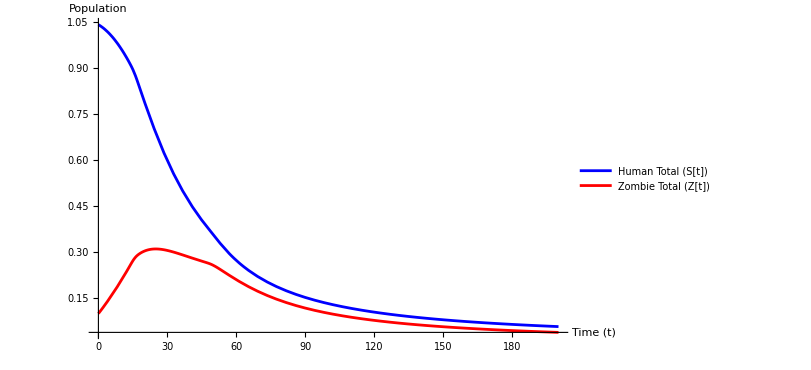

```mathematica
S[t_]:=sols[[3]][t]+sols[[4]][t]+sols[[6]][t]; (*Shm+Shw+Sm*)
Z[t_]:=sols[[1]][t]+sols[[2]][t];               (*Szn+Szp*)


Plot[{S[t],Z[t]},{t,0,200},PlotLegends->{"Human Total (S[t])","Zombie Total (Z[t])"},PlotStyle->{Blue,Red},AxesLabel->{"Time (t)","Population"},PlotRange->All, ImageSize->600]
```

vectorField

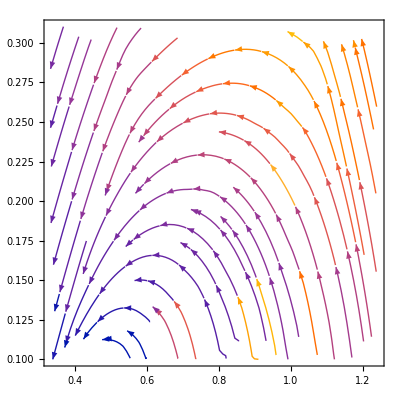

```mathematica
vectorField/. {S[t]->1,Z[t]->1}
data1=Table[{{sols[[7]][t],sols[[8]][t]},{sols[[7]]'[t],sols[[8]]'[t]}},{t,0,100,0.5}];
ListStreamPlot[data1]
```

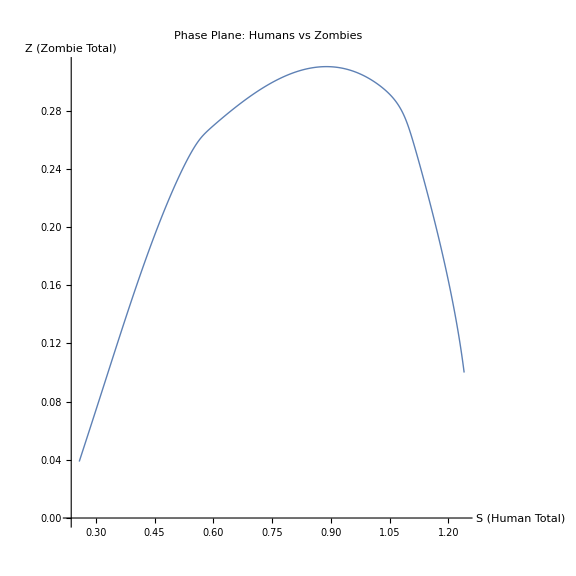

```mathematica
(*Define S[t] and Z[t] from solutions*)S[t_]:=sols[[7]][t]; (*Human population,from Shm+Shw+Sm*)
Z[t_]:=sols[[8]][t]; (*Zombie population,from Szn+Szp*)

(*Generate phase plane data for S[t] and Z[t]*)
phaseData=Table[{S[t],Z[t]},{t,0,200,0.1}];

(*Plot the phase plane*)
ListLinePlot[phaseData,AxesLabel->{"S (Human Total)","Z (Zombie Total)"},PlotLabel->"Phase Plane: Humans vs Zombies",PlotRange->All,AspectRatio->1,ImageSize->Large,PlotStyle->Thick]
```

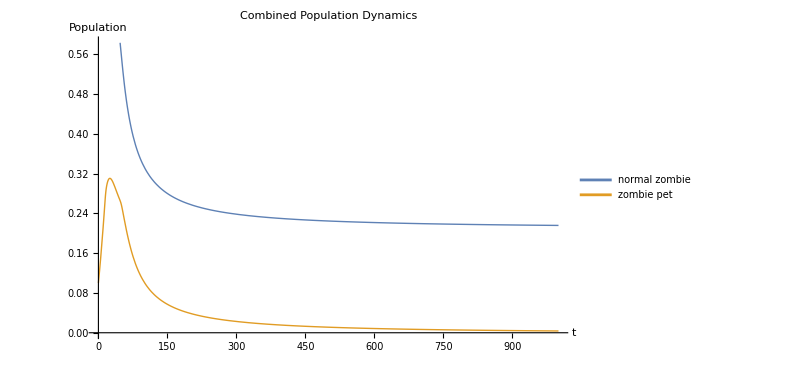

```mathematica
Plot[Evaluate[{sols[[7]][t],sols[[8]][t]}],{t,0,1000},PlotLegends->{"normal zombie","zombie pet"},PlotStyle->{Thick,Thick },AxesLabel->{"t","Population"},PlotLabel->"Combined Population Dynamics",ImageSize->600]
```

```mathematica
Manipulate[LogLogPlot[Evaluate[{sols[[1]][t],sols[[2]][t],sols[[3]][t],sols[[4]][t],sols[[5]][t],sols[[6]][t]}],{t,1,100},(*Ensure the range avoids log(0) errors*)PlotLegends->{"normal zombie","zombie pet","worker","mole","soldier"},PlotStyle->{Thick,{Thick,Dotted},Thick,Thick,Thick,Thick},AxesLabel->{"log(t)","log(Population)"},PlotLabel->"Combined Population Dynamics (Log-Log Scale)",ImageSize->600],{{Tmax,1000,"Time Range"},100,10,000,100},{{γ1,0.1,"γ1"},0.1,1,0.1}]
```